# Smarticles

## Friction - force balance

### Single link, 1D

```mathematica
$Assumptions=And@@(#>0&/@{Fp,L,r,Fn})
sol=Solve[{Fp L (r-d)==Fn/2(L^2+d^2),Fp==-Fn(d/L)},{d,Fp}]//FullSimplify
sol/.r->L//N//FullSimplify
```

Fp>0&&L>0&&r>0&&Fn>0

(d→r-√(L^2+r^2) | Fp→(Fn (-r+√(L^2+r^2)))/L
d→r+√(L^2+r^2) | Fp→-(Fn (r+√(L^2+r^2)))/L)

(d→-0.414214 L | Fp→0.414214 Fn
d→2.41421 L | Fp→-2.41421 Fn)

### 2-link, 2D - line friction

#### figuring it out

```mathematica
$Assumptions=And@@(#∈Reals&/@{F,B,A,r,Fn,px,py,pr,pθ,α,θ,l1,l2})
```

F∈Reals&&B∈Reals&&A∈Reals&&r∈Reals&&Fn∈Reals&&px∈Reals&&py∈Reals&&pr∈Reals&&pθ∈Reals&&α∈Reals&&θ∈Reals&&l1∈Reals&&l2∈Reals

Friction Forces:

```mathematica
Integrate[-py/(√((px-x)^2+py^2)),{x,-B/2,B/2}]
Integrate[(px-x)/(√((px-x)^2+py^2)),{x,-B/2,B/2}]
Ff=Fn/B{%%,%}//FullSimplify
```

-py Log[(B+2 px+√((B+2 px)^2+4 py^2))/(-B+2 px+√((B-2 px)^2+4 py^2))]

1/2 (-√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))

{1/B Fn py (Log[-B+2 px+√((B-2 px)^2+4 py^2)]-Log[B+2 px+√((B+2 px)^2+4 py^2)]),(Fn (-√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2)))/(2 B)}

```mathematica
Simplify[Ff/.py->0,Assumptions->B>0&& Abs[px]<B/2]
Simplify[Ff/.py->0,Assumptions->B>0&& px<-B/2]
```

{0,(2 Fn px)/B}

{0,-Fn}

Friction Torque

```mathematica
τf=Fn/B Integrate[√((px-x)^2+py^2) ,{x,-B/2,B/2}]//FullSimplify
```

1/(8 B)Fn (2 px (-√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))+B (√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))+4 py^2 Log[(B+2 px+√((B+2 px)^2+4 py^2))/(-B+2 px+√((B-2 px)^2+4 py^2))])

```mathematica
Plot3D[τf/.{B->1,Fn->1},{px,-0.5,0.5},{py,-0.5,0.5},ColorFunction->"Rainbow"]
Series[τf,{B,0,2}]//FullSimplify
τf/.{px->0,py-> 0}//FullSimplify
```

-Graphics3D-

Fn √(px^2+py^2)+(Fn py^2 B^2)/(24 (px^2+py^2)^(3/2))+O[B]^3

1/4 Fn Abs[B]

```mathematica
τ=-({f Cos[θ],f Sin[θ],0}×{B/2+A Cos[α]-px,A Sin[α]-py,0})[[3]]//FullSimplify
τ/.{α->0,θ->π/2}
τ/.{α->π/2,θ->0}
```

1/2 f (2 py Cos[θ]-2 A Sin[α-θ]+(B-2 px) Sin[θ])

1/2 f (2 A+B-2 px)

1/2 f (-2 A+2 py)

Force balance (here f ≡ F/Fn)

```mathematica
syst={f Cos[θ]==-Ff[[1]]/Fn,f Sin[θ]==-Ff[[2]]/Fn,τf/Fn==τ}
(*/.{√((B-2 px)^2+4 py^2)->l1,√((B+2 px)^2+4 py^2)->l2}*)
Solve[%,{px,py,f}]
```

{f Cos[θ]==1/B py (Log[-B+2 px+√((B-2 px)^2+4 py^2)]-Log[B+2 px+√((B+2 px)^2+4 py^2)]),f Sin[θ]==-(-√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))/(2 B),1/(8 B)(2 px (-√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))+B (√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))+4 py^2 Log[(B+2 px+√((B+2 px)^2+4 py^2))/(-B+2 px+√((B-2 px)^2+4 py^2))])==1/2 f (2 py Cos[θ]-2 A Sin[α-θ]+(B-2 px) Sin[θ])}

$Aborted

```mathematica
FullSimplify[syst/.{py->0,θ->π/2},Assumptions->B>0&&Abs[px]<B/2]
Solve[%,{px,f}]//FullSimplify
%/.A->0//N//FullSimplify
%%/.{α->π,A->B/2-a}//FullSimplify
%/.{a->B/2}//N//FullSimplify
```

{True,B f+2 px==0,B (B (-1+2 f)+4 A f Cos[α])==4 px (B f+px)}

(px→1/4 (2 B+4 A Cos[α]+2 √(B^2+(B+2 A Cos[α])^2)) | f→-(2 B+4 A Cos[α]+2 √(B^2+(B+2 A Cos[α])^2))/(2 B)
px→1/2 (B+2 A Cos[α]-√(B^2+(B+2 A Cos[α])^2)) | f→(-2 B-4 A Cos[α]+2 √(B^2+(B+2 A Cos[α])^2))/(2 B))

(px→1.20711 B | f→-2.41421
px→-0.207107 B | f→0.414214)

(px→a+1/2 √(4 a^2+B^2) | f→-(2 a+√(4 a^2+B^2))/B
px→a-1/2 √(4 a^2+B^2) | f→(-2 a+√(4 a^2+B^2))/B)

(px→1.20711 B | f→-2.41421
px→-0.207107 B | f→0.414214)

```mathematica
FullSimplify[syst/.{py->0,θ->π/2},Assumptions->B>0&&px<-B/2]
%/.{α->π,A->B/2-a}
```

{True,f==1,(B f)/2+px+A f Cos[α]==f px}

{True,f==1,-(-a+B/2) f+(B f)/2+px==f px}

```mathematica
{syst/.{√((B-2 px)^2+4 py^2)->2 l1,√((B+2 px)^2+4 py^2)->2 l2},
{√((B-2 px)^2+4 py^2)==2l1,√((B+2 px)^2+4 py^2)==2l2}}//Flatten
Solve[%,{px,py,F,l1,l2}]
```

{f Cos[θ]==(py (Log[-B+2 l1+2 px]-Log[B+2 l2+2 px]))/B,f Sin[θ]==-(-2 l1+2 l2)/(2 B),(B (2 l1+2 l2)+2 (-2 l1+2 l2) px+4 py^2 Log[(B+2 l2+2 px)/(-B+2 l1+2 px)])/(8 B)==1/2 f (2 py Cos[θ]-2 A Sin[α-θ]+(B-2 px) Sin[θ]),√((B-2 px)^2+4 py^2)==2 l1,√((B+2 px)^2+4 py^2)==2 l2}

$Aborted

```mathematica
Do[
solTmp=FindRoot[syst//.{B->1.,A->1.,α->π/2,θ->-1.π+α}//N
,{{px,RandomReal[]-0.5,-0.5,0.5},{py,(RandomReal[]-0.5)*1,-20,20},{f,RandomReal[],-1,1}}];
Print[{ii,solTmp}];
If[-1<(f/.solTmp)<1&&-0.5<(px/.solTmp)<0.5,Break[]]
,{ii,10}]
```

{1,{px→-0.207107,py→-8.90037×10^-8,f→-0.414214}}

```mathematica
Plot3D[
{py}/.FindRoot[syst/.{B->1.,A->1,θ->τ+α}//N
,{{px,0.1,-1.5,1.5},{py,0.1,-20,20},{f,0.1,-1,1}}]//Evaluate,{α,0,π},{τ,-3π/2,-π/2},PlotPoints->10,MaxRecursion->2,PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Log[(B+2 px+√((B+2 px)^2+4 py^2))/(-B+2 px+√((B-2 px)^2+4 py^2))]
FullSimplify[Series[%,{py,0,2},Assumptions->Abs[px]<B/2]]
FullSimplify[Series[%%,{py,∞,2},Assumptions->Abs[px]<B/2]]
Series[%%%,{B,0,2}]
```

Log[(B+2 px+√((B+2 px)^2+4 py^2))/(-B+2 px+√((B-2 px)^2+4 py^2))]

Log[((B+2 px) Abs[B-2 px])/py^2]+(1/(B-2 px)^2+1/(B+2 px)^2) py^2+O[py]^3

B/py+O[1/py]^3

B/(√(px^2+py^2))+O[B]^3

```mathematica
FullSimplify[Solve[{√((B-2 px)^2+4 py^2)==l1,√((B+2 px)^2+4 py^2)==l2},{px,py}]
,Assumptions->l1>0&&l2>0]
```

(px→(-l1^2+l2^2)/(8 B) | py→-(√(-16 B^4-(l1^2-l2^2)^2+8 B^2 (l1^2+l2^2)))/(8 B)
px→(-l1^2+l2^2)/(8 B) | py→(√(-16 B^4-(l1^2-l2^2)^2+8 B^2 (l1^2+l2^2)))/(8 B))

```mathematica
Series[syst,{py,0,1}]
Solve[%//Normal,{px,py,F}]
Series[syst,{py,∞,1}]
```

{F Cos[θ]==((Fn Log[2 B+4 px]-Fn Log[-B+2 px+Abs[B-2 px]]) py)/B+O[py]^2,F Sin[θ]==(Fn √((B-2 px)^2)-Fn √((B+2 px)^2))/(2 B)+O[py]^2,1/(8 B)(B Fn √((B-2 px)^2)-2 Fn √((B-2 px)^2) px+B Fn √((B+2 px)^2)+2 Fn px √((B+2 px)^2))+O[py]^2==(-A F Sin[α-θ]+1/2 B F Sin[θ]-F px Sin[θ])+F Cos[θ] py+O[py]^2}

$Aborted

{F Cos[θ]==Fn+O[1/py]^2,F Sin[θ]==-(Fn px)/py+O[1/py]^2,Fn py+(B^2 Fn+12 Fn px^2)/(24 py)+O[1/py]^2==F Cos[θ] py+(-A F Sin[α-θ]+1/2 B F Sin[θ]-F px Sin[θ])+O[1/py]^2}

```mathematica
Series[syst,{B,0,1}]//Normal//FullSimplify
sol1=Solve[%,{px,py,f}]//Simplify
```

{py/(√(px^2+py^2))+f Cos[θ]==0,px/(√(px^2+py^2))+f Sin[θ]==0,2 (√(px^2+py^2)+A f Sin[α-θ])==2 f py Cos[θ]+f (B-2 px) Sin[θ]}

(px→-1/4 Sec[θ] (-2 A Sin[α-θ]+B Sin[θ]) Tan[θ] | py→-1/4 Sec[θ] (-2 A Sin[α-θ]+B Sin[θ]) | f→-1
px→-1/4 Sec[θ] (-2 A Sin[α-θ]+B Sin[θ]) Tan[θ] | py→-1/4 Sec[θ] (-2 A Sin[α-θ]+B Sin[θ]) | f→1)

```mathematica
sol1=Solve[{py/(√(px^2+py^2))+f Cos[θ]==0,px/(√(px^2+py^2))+f Sin[θ]==0,2 (√(px^2+py^2)+(B^2 py^2)/(24 (px^2+py^2)^(3/2))+A f Sin[α-θ])==2 f py Cos[θ]+f (B-2 px) Sin[θ]},{px,py,f}]//Simplify
```

(px→-1/48 Sec[θ] (√6 √(12 A^2+12 A B Cos[α]-12 A B Cos[α-2 θ]-12 A^2 Cos[2 α-2 θ]-7 B^2 Cos[2 θ]-B^2 Cos[4 θ])-12 A Sin[α-θ]+6 B Sin[θ]) Tan[θ] | py→-1/48 Sec[θ] (√6 √(12 A^2+12 A B Cos[α]-12 A B Cos[α-2 θ]-12 A^2 Cos[2 α-2 θ]-7 B^2 Cos[2 θ]-B^2 Cos[4 θ])-12 A Sin[α-θ]+6 B Sin[θ]) | f→(Sec[θ]^2 (√(12 A^2+12 A B Cos[α]-12 A B Cos[α-2 θ]-12 A^2 Cos[2 α-2 θ]-7 B^2 Cos[2 θ]-B^2 Cos[4 θ])-2 √6 A Sin[α-θ]+√6 B Sin[θ]))/(√(-Sec[θ]^4 (-24 A^2-3 B^2-24 A B Cos[α]+24 A B Cos[α-2 θ]+24 A^2 Cos[2 α-2 θ]+10 B^2 Cos[2 θ]+B^2 Cos[4 θ]+4 √6 A √(12 A^2+12 A B Cos[α]-12 A B Cos[α-2 θ]-12 A^2 Cos[2 α-2 θ]-7 B^2 Cos[2 θ]-B^2 Cos[4 θ]) Sin[α-θ]-2 √6 B √(12 A^2+12 A B Cos[α]-12 A B Cos[α-2 θ]-12 A^2 Cos[2 α-2 θ]-7 B^2 Cos[2 θ]-B^2 Cos[4 θ]) Sin[θ])))
px→1/48 Sec[θ] (√6 √(12 A^2+12 A B Cos[α]-12 A B Cos[α-2 θ]-12 A^2 Cos[2 α-2 θ]-7 B^2 Cos[2 θ]-B^2 Cos[4 θ])+12 A Sin[α-θ]-6 B Sin[θ]) Tan[θ] | py→1/48 Sec[θ] (√6 √(12 A^2+12 A B Cos[α]-12 A B Cos[α-2 θ]-12 A^2 Cos[2 α-2 θ]-7 B^2 Cos[2 θ]-B^2 Cos[4 θ])+12 A Sin[α-θ]-6 B Sin[θ]) | f→-(Sec[θ]^2 (√(12 A^2+12 A B Cos[α]-12 A B Cos[α-2 θ]-12 A^2 Cos[2 α-2 θ]-7 B^2 Cos[2 θ]-B^2 Cos[4 θ])+2 √6 A Sin[α-θ]-√6 B Sin[θ]))/(√(-Sec[θ]^4 (-24 A^2-3 B^2-24 A B Cos[α]+24 A B Cos[α-2 θ]+24 A^2 Cos[2 α-2 θ]+10 B^2 Cos[2 θ]+B^2 Cos[4 θ]-4 √6 A √(12 A^2+12 A B Cos[α]-12 A B Cos[α-2 θ]-12 A^2 Cos[2 α-2 θ]-7 B^2 Cos[2 θ]-B^2 Cos[4 θ]) Sin[α-θ]+2 √6 B √(12 A^2+12 A B Cos[α]-12 A B Cos[α-2 θ]-12 A^2 Cos[2 α-2 θ]-7 B^2 Cos[2 θ]-B^2 Cos[4 θ]) Sin[θ]))))

```mathematica
Series[syst,{B,0,2}]//FullSimplify
(*sol2=Solve[%//Normal,{px,py,f}]//Simplify*)
FullSimplify[%/.{px->pr Cos[pθ],py->pr Sin[pθ]}/.pθ->ArcSin[pθ],Assumptions->pr>0]
sol2=Solve[%//Normal,{pr,pθ,f}]
%//Simplify
```

{f Cos[θ]==-py/(√(px^2+py^2))+(py (-2 px^2+py^2) B^2)/(24 (px^2+py^2)^(5/2))+O[B]^3,f Sin[θ]==-px/(√(px^2+py^2))+(px py^2 B^2)/(8 (px^2+py^2)^(5/2))+O[B]^3,(√(px^2+py^2)-f py Cos[θ]+A f Sin[α-θ]+f px Sin[θ])-1/2 (f Sin[θ]) B+(py^2 B^2)/(24 (px^2+py^2)^(3/2))+O[B]^3==0}

{(pθ+f Cos[θ])+((2 pθ-3 pθ^3) B^2)/(24 pr^2)+O[B]^3==0,(√(1-pθ^2)+f Sin[θ])-((pθ^2 √(1-pθ^2)) B^2)/(8 pr^2)+O[B]^3==0,(pr-f pr pθ Cos[θ]+A f Sin[α-θ]+f pr √(1-pθ^2) Sin[θ])-1/2 (f Sin[θ]) B+(pθ^2 B^2)/(24 pr)+O[B]^3==0}

$Aborted

$Aborted

```mathematica
sol1/.{B->1,A->1,α->π,θ->-π}//N
```

(px→0. | py→0.+0.144338 ⅈ | f→1.
px→0. | py→0.-0.144338 ⅈ | f→-1.)

```mathematica
Series[syst,{B,∞,2}]//FullSimplify
```

```mathematica
Plot3D[
px/.sol1[[1]]/.{B->1.,A->0.1,θ->τ+α}//N//Re,{α,0,π/2},{τ,-3π/2,-π/2},PlotPoints->10,MaxRecursion->1,ColorFunction->"Rainbow",PlotStyle->Directive[Opacity[1]]]
```

-Graphics3D-

```mathematica
Plot3D[
If[-0.5<#[[2]]<0.5,#[[2]],#[[1]]]&[py/.sol1/.{B->1.,A->0.1,θ->τ+α}//N//Re],{α,0,π/2},{τ,-3π/2,-π/2},PlotPoints->10,MaxRecursion->1,ColorFunction->"Rainbow",PlotStyle->Directive[Opacity[1]],PlotRange->{-0.5,0.5}]
```

-Graphics3D-

```mathematica
Series[τf,{B,∞,0}]
FullSimplify[Series[Ff,{B,∞,0}],Assumptions->B>0]
systB=FullSimplify[{f Cos[θ]==%[[1]]/Fn,f Sin[θ]==-%[[2]]/Fn,%%/Fn==τ}//Normal,Assumptions->B>0]
eqpy=Eliminate[%,{f,px}]//FullSimplify
```

(Fn B)/4+O[1/B]^1

{(Fn py Log[py^2/B^2])/B+O[1/B]^2,(2 Fn px)/B+O[1/B]^2}

{B f Cos[θ]==py Log[py^2/B^2],2 px+B f Sin[θ]==0,4 f py Cos[θ]+2 f (B-2 px) Sin[θ]==B+4 A f Sin[α-θ]}

py Log[py^2/B^2] (2 py Log[py^2/B^2] Sin[θ]^2+2 Cos[θ] (2 py Cos[θ]-2 A Sin[α-θ]+B Sin[θ]))==B^2 Cos[θ]^2

```mathematica
eqpy=py Log[py^2/B^2] (2 py Log[py^2/B^2] Sin[θ]^2+2 Cos[θ] (2 py Cos[θ]-2 A Sin[α-θ]+B Sin[θ]))-B^2 Cos[θ]^2;
eqpySer=Series[eqpy,{py,0.001,1}]//Normal
solpy=Solve[0==%//Normal//FullSimplify,py]
%/.{B->1,A->1,α->0.2π,θ->0.4π}
```

-B^2 Cos[θ]^2+4.×10^-6 Cos[θ]^2 Log[(1.×10^-6)/B^2]-0.004 A Cos[θ] Log[(1.×10^-6)/B^2] Sin[α-θ]+0.002 B Cos[θ] Log[(1.×10^-6)/B^2] Sin[θ]+2.×10^-6 Log[(1.×10^-6)/B^2]^2 Sin[θ]^2+(-0.001+py) (0.008 Cos[θ]^2+0.008 Cos[θ]^2 Log[(1.×10^-6)/B^2]-8. A Cos[θ] Sin[α-θ]-4 A Cos[θ] Log[(1.×10^-6)/B^2] Sin[α-θ]+4. B Cos[θ] Sin[θ]+2 B Cos[θ] Log[(1.×10^-6)/B^2] Sin[θ]+0.008 Log[(1.×10^-6)/B^2] Sin[θ]^2+0.004 Log[(1.×10^-6)/B^2]^2 Sin[θ]^2)

(py→(0.000047262 Cos[θ]^2-1. B^2 Cos[θ]^2-4.×10^-6 Cos[θ]^2 Log[1/B^2]+0.008 A Cos[θ] Sin[α-1. θ]-0.004 B Cos[θ] Sin[θ]-0.000271213 Sin[θ]^2+0.000047262 Log[1/B^2] Sin[θ]^2-2.×10^-6 Log[1/B^2]^2 Sin[θ]^2)/(0.102524 Cos[θ]^2-0.008 Cos[θ]^2 Log[1/B^2]-47.262 A Cos[θ] Sin[α-1. θ]+4. A Cos[θ] Log[1/B^2] Sin[α-1. θ]+23.631 B Cos[θ] Sin[θ]-2. B Cos[θ] Log[1/B^2] Sin[θ]-0.652949 Sin[θ]^2+0.102524 Log[1/B^2] Sin[θ]^2-0.004 Log[1/B^2]^2 Sin[θ]^2))

(py→-0.00657992)

```mathematica
Manipulate[
Plot[{eqpy,eqpySer}//.{B->1,A->0.5,α->0.π,θ->α+τ}//Evaluate,{py,-1.5,1.5},PlotRange->{-3,3}],{τ,-3π/2,-π/2}]
```

```mathematica
FindRoot[0==eqpy/.{A-> 1.,B-> 1.}//Evaluate,{py,0}]
```

FindRoot[0==-1. Cos[θ]^2+py Log[1. py^2] (2 py Log[1. py^2] Sin[θ]^2+2 Cos[θ] (2 py Cos[θ]-2. Sin[α-θ]+1. Sin[θ])),{py,0}]

```mathematica
FindRoot[eqpy==0/.repl1/.{α->π/2,τ->-π}//Evaluate,{py,0.1}]
```

{py→4.70133×10^-9}

```mathematica
Solve[systB[[1;;2]],{px,f}]
```

(px→-1/2 py Log[py^2/B^2] Tan[θ] | f→(py Log[py^2/B^2] Sec[θ])/B)

```mathematica
repl1={B->1.,A->0.2,θ->τ+α};
({{px->-1/2 py Log[py^2/B^2] Max[Min[Tan[θ],3],-3], f->(py Log[py^2/B^2] Sec[θ])/B}});
Plot3D[
{py}/.%/.FindRoot[0.== eqpy/.repl1//Evaluate,{py,1.,-1.5,1.5}]/.repl1,{α,0,π/2},{τ,-3π/2,-π/2},PlotPoints->10,MaxRecursion->2,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
repl1={B->1.,A->0.,θ->τ};
({{px->-1/2 py Log[py^2/B^2] Max[Min[Tan[θ],3],-3], f->(py Log[py^2/B^2] Sec[θ])/B}});
Plot3D[
{py}/.%/.solpy/.repl1,{α,0,π/2},{τ,-3π/2,-π/2},PlotPoints->10,MaxRecursion->2,ColorFunction->"Rainbow",PlotRange->{-1,1}*0.08]
```

-Graphics3D-

```mathematica
Plot3D[
{py}/.FindRoot[syst/.repl1//N
,{{px,0.1,-1.5,1.5},{py,0.01,-20,20},{f,0.1,-1,1}}]//Evaluate,{α,0,π/2},{τ,-3π/2,-π/2},PlotPoints->10,MaxRecursion->2,PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Plot3D[
{py}/.FindRoot[systB/.repl1//N
,{{px,0.1,-1.5,1.5},{py,0.1,-20,20},{f,0.1,-1,1}}]//Evaluate,{α,0,π/2},{τ,-3π/2,-π/2},PlotPoints->10,MaxRecursion->2,PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
repl1={B->1.,θ->α+π/2};
({{px->-1/2 py Log[py^2/B^2] Max[Min[Tan[θ],3],-3], f->(py Log[py^2/B^2] Sec[θ])/B}});
Plot3D[
{f}/.%/.solpy/.repl1,{α,0,π/2},{A,0,1},PlotPoints->10,MaxRecursion->2,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Plot3D[
{f}/.FindRoot[syst/.repl1//N
,{{px,0.1,-1.5,1.5},{py,0.01,-20,20},{f,0.1,-1,1}}]//Evaluate,{α,0,π/2},{A,0,1},PlotPoints->10,MaxRecursion->2,PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Clean

```mathematica
$Assumptions=And@@(#∈Reals&/@{F,B,A,r,Fn,px,py,pr,pθ,α,θ,l1,l2})&&B>0&&Abs[px]<B/2&&py≠0
```

F∈Reals&&B∈Reals&&A∈Reals&&r∈Reals&&Fn∈Reals&&px∈Reals&&py∈Reals&&pr∈Reals&&pθ∈Reals&&α∈Reals&&θ∈Reals&&l1∈Reals&&l2∈Reals&&B>0&&Abs[px]<B/2&&py≠0

Friction forces:

```mathematica
Integrate[-py/(√((px-x)^2+py^2)),{x,-B/2,B/2}]
Integrate[(px-x)/(√((px-x)^2+py^2)),{x,-B/2,B/2}]
Ff={%%,%}//FullSimplify
```

-py Log[(B+2 px+√((B+2 px)^2+4 py^2))/(-B+2 px+√((B-2 px)^2+4 py^2))]

(B^2 (√(B^2-4 B px+4 (px^2+py^2))-√(B^2+4 B px+4 (px^2+py^2)))+4 (px^2+py^2) (√(B^2-4 B px+4 (px^2+py^2))-√(B^2+4 B px+4 (px^2+py^2)))+4 B px (√(B^2-4 B px+4 (px^2+py^2))+√(B^2+4 B px+4 (px^2+py^2))))/(2 √(B^4-8 B^2 (px^2-py^2)+16 (px^2+py^2)^2))+px Log[(B+2 px+√((B+2 px)^2+4 py^2))/(-B+2 px+√((B-2 px)^2+4 py^2))]-px Log[1/2 (B-2 px+√(B^2-4 B px+4 (px^2+py^2)))]-px Log[2/(-B-2 px+√(B^2+4 B px+4 (px^2+py^2)))]

{py (Log[-B+2 px+√((B-2 px)^2+4 py^2)]-Log[B+2 px+√((B+2 px)^2+4 py^2)]),1/2 (-√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))}

```mathematica
Simplify[Ff/.py->0,Assumptions->B>0&& Abs[px]<B/2]
Simplify[Ff/.py->0,Assumptions->B>0&& px<-B/2]
```

{0,2 px}

{0,-B}

Friction Torque

```mathematica
τf= Integrate[√((px-x)^2+py^2) ,{x,-B/2,B/2}]//FullSimplify
```

1/8 (2 px (-√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))+B (√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))+4 py^2 (-Log[-B+2 px+√((B-2 px)^2+4 py^2)]+Log[B+2 px+√((B+2 px)^2+4 py^2)]))

```mathematica
Plot3D[τf/.{B->1,Fn->1},{px,-0.5,0.5},{py,-0.5,0.5},ColorFunction->"Rainbow"]
Series[τf,{B,0,2}]//FullSimplify
τf/.{px->0,py-> 0}//FullSimplify
```

-Graphics3D-

Fn √(px^2+py^2)+(Fn py^2 B^2)/(24 (px^2+py^2)^(3/2))+O[B]^3

1/4 Fn Abs[B]

Applied torque:

```mathematica
τa=-({f Cos[θ],f Sin[θ],0}×{B/2+A Cos[α]-px,A Sin[α]-py,0})[[3]]//FullSimplify
τa/.{α->0,θ->π/2}
τa/.{α->π/2,θ->0}
```

1/2 f (2 py Cos[θ]-2 A Sin[α-θ]+(B-2 px) Sin[θ])

1/2 f (2 A+B-2 px)

1/2 f (-2 A+2 py)

Force balance system (here f ≡ F/Fn)

```mathematica
syst={f Cos[θ]==-Ff[[1]],f Sin[θ]==-Ff[[2]],τa==τf}
```

{f Cos[θ]==-py (Log[-B+2 px+√((B-2 px)^2+4 py^2)]-Log[B+2 px+√((B+2 px)^2+4 py^2)]),f Sin[θ]==1/2 (√((B-2 px)^2+4 py^2)-√((B+2 px)^2+4 py^2)),1/2 f (2 py Cos[θ]-2 A Sin[α-θ]+(B-2 px) Sin[θ])==1/8 (2 px (-√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))+B (√((B-2 px)^2+4 py^2)+√((B+2 px)^2+4 py^2))+4 py^2 (-Log[-B+2 px+√((B-2 px)^2+4 py^2)]+Log[B+2 px+√((B+2 px)^2+4 py^2)]))}

```mathematica
FullSimplify[syst/.{py->0,θ->π/2},Assumptions->B>0&&Abs[px]<B/2]
Solve[%,{px,f}]//FullSimplify
%/.A->0//N//FullSimplify
%%/.{α->π,A->B/2-x}/.B->1//FullSimplify
%/.{x->1/2}//N//FullSimplify
```

{True,f==-2 px,B^2+4 px (f+px)==2 f (B+2 A Cos[α])}

(px→1/4 (2 B+4 A Cos[α]+2 √(B^2+(B+2 A Cos[α])^2)) | f→1/2 (-2 B-4 A Cos[α]-2 √(B^2+(B+2 A Cos[α])^2))
px→1/2 (B+2 A Cos[α]-√(B^2+(B+2 A Cos[α])^2)) | f→1/2 (-2 B-4 A Cos[α]+2 √(B^2+(B+2 A Cos[α])^2)))

(px→1.20711 B | f→-2.41421 B
px→-0.207107 B | f→0.414214 B)

(px→x+1/2 √(1+4 x^2) | f→-2 x-√(1+4 x^2)
px→x-1/2 √(1+4 x^2) | f→-2 x+√(1+4 x^2))

(px→1.20711 | f→-2.41421
px→-0.207107 | f→0.414214)

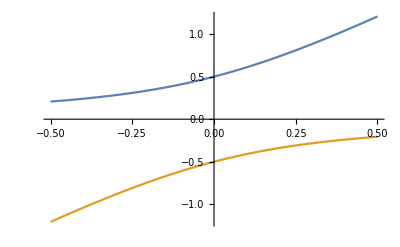

```mathematica
Plot[{x+1/2 √(1+4 x^2),x-1/2 √(1+4 x^2)},{x,-0.5,0.5}]
```

Solve numerically:

```mathematica
Do[
solTmp=FindRoot[syst//.{B->1.,A->1.,α->π/2,θ->-1.5π+α}//N
,{{px,RandomReal[]-0.5,-0.5,0.5},{py,(RandomReal[]-0.5)*1,-20,20},{f,RandomReal[],-1,1}}];
Print[{ii,solTmp}];
If[-1<(f/.solTmp)<1&&-0.5<(px/.solTmp)<0.5,Break[]]
,{ii,10}]
```

{1,{px→-1.77258×10^-17,py→-0.0374414,f→0.246093}}

```mathematica
Plot3D[
{f}/.FindRoot[syst/.{B->1.,A->1,θ->τ+α}//N
,{{px,0.1,-1.5,1.5},{py,0.01,-20,20},{f,0.1,-1,1}}]//Evaluate,{α,0,π},{τ,-3π/2,-π/2},PlotPoints->10,MaxRecursion->2,PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

Expand system for large B

```mathematica
Series[τf,{B,∞,0}]
FullSimplify[Series[Ff,{B,∞,0}],Assumptions->B>0]
systB=FullSimplify[{f Cos[θ]==-%[[1]],f Sin[θ]==-%[[2]],%%==τa}//Normal,Assumptions->B>0]
eqpy=Eliminate[%,{f,px}]//FullSimplify
```

B^2/4+1/2 (2 px^2+py^2+py^2 Log[2]+py^2 Log[B]-py^2 Log[(2 py^2)/B])+O[1/B]^1

{py Log[py^2/B^2]+O[1/B]^1,2 px+O[1/B]^1}

{f Cos[θ]+py Log[py^2/B^2]==0,f Sin[θ]==-2 px,B^2+4 px^2+2 py^2+4 py^2 Log[B]+4 A f Sin[α-θ]==4 f py Cos[θ]+2 py^2 Log[py^2]+2 f (B-2 px) Sin[θ]}

Cos[θ] (Cos[θ] (B^2+2 py^2+py^2 Log[py^4/B^4])+2 py Log[py^2/B^2] (-2 A Sin[α-θ]+B Sin[θ]))==py^2 Log[py^2/B^2]^2 Sin[θ]^2

```mathematica
Solve[systB,{f,px,py}]
```

$Aborted

Numerically:

```mathematica
repl1={B->1.,A->0.5,θ->τ};
({{px->1/2 py Log[py^2/B^2] 1/2 py Log[py^2/B^2] Tan[θ], f->-py Log[py^2/B^2] Sec[θ]}});
Plot3D[
{px}/.%/.FindRoot[0.== eqpy/.repl1//Evaluate,{py,0.01,-1.5,1.5}]/.repl1,{α,0,π/2},{τ,-3π/2,-π/2},PlotPoints->10,MaxRecursion->2,ColorFunction->"Rainbow"]
```

-Graphics3D-

Further expand around small py and solve analytically:

```mathematica
eqpy=Cos[θ] (Cos[θ] (B^2+2 py^2+py^2 Log[py^4/B^4])+2 py Log[py^2/B^2] (-2 A Sin[α-θ]+B Sin[θ]))-py^2 Log[py^2/B^2]^2 Sin[θ]^2;
eqpySer=Series[eqpy/.B->1,{py,0.0001,1}]//Normal
solpy=Solve[0==%//Normal//FullSimplify,py]//FullSimplify
%/.{B->1,A->1,α->0.2π,θ->0.4π}
```

1. Cos[θ]^2+0.00736827 A Cos[θ] Sin[α-θ]-0.00368414 Cos[θ] Sin[θ]-3.39321×10^-6 Sin[θ]^2+(-0.0001+py) (-0.00656827 Cos[θ]^2+65.6827 A Cos[θ] Sin[α-θ]-32.8414 Cos[θ] Sin[θ]-0.060496 Sin[θ]^2)

(py→0.0000439101+(Cos[θ] (152.247 Cos[θ]+0.560899 A Sin[α-1. θ]-0.280449 Sin[θ]))/(1. Cos[θ]^2+9.21034 Sin[θ]^2+Cos[θ] (-10000. A Sin[α-1. θ]+5000. Sin[θ])))

(py→0.0044012)

```mathematica
Manipulate[
Plot[{eqpy,eqpySer}//.{B->1,A->0.5,α->0.π,θ->α+τ}//Evaluate,{py,-4.5,4.5},PlotRange->{-3,3},Epilog->{Red,PointSize@Large,Point[{py,0}/.solpy/.sc->0.081//.{A->0.5,θ->α+τ,α->0.}]}],{τ,-3π/2,-π/2}]
```

Simplify the approximation for py:

```mathematica
solpy={py->5.475605008012312*^-6+(Cos[θ] (1189.0125202685813 Cos[θ]+0.5475605008012311 A Sin[α-1. θ]-0.27378025040061554 Sin[θ]))/(0*1. Cos[θ]^2+0*11.51292546497023 Sin[θ]^2+Cos[θ] (-99999.99999999999 A Sin[α-1. θ]+49999.99999999999 Sin[θ]))}//FullSimplify
```

{py→1/(-84.1034 A Sec[θ] Sin[α-1. θ]+42.0517 Tan[θ])}

```mathematica
Limit[py/.solpy,θ->π/2]//FullSimplify
```

0.

```mathematica
solpy={py->sc/(-2 A Sec[θ] Sin[α-1. θ]+Tan[θ])}
```

{py→sc/(-2 A Sec[θ] Sin[α-1. θ]+Tan[θ])}

Regularize (make differentiable) the solution for px and f:

```mathematica
Solve[systB[[1;;2]],{px,f}]
```

(px→1/2 py Log[py^2/B^2] Tan[θ] | f→-py Log[py^2/B^2] Sec[θ])

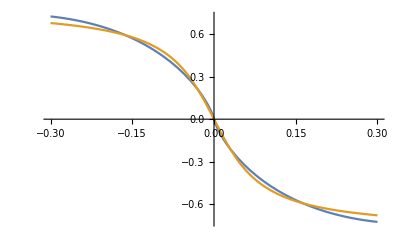

```mathematica
Plot[{py Log[py^2],-0.5ArcTan[15py]}//Evaluate,{py,-0.3,0.3}]
```

Get quantitative agreement with numerical solution (find the scaling factor):

{px→-0.3 ArcTan[10 py] Tan[θ],f→0.6 ArcTan[10 py] Sec[θ]}

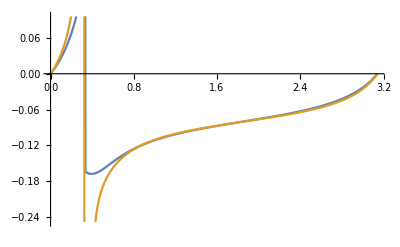
{-Graphics3D-,-Graphics-}

```mathematica
repl1={B->1.,A->1,θ->τ,α->0.5};
{px->1/2 Tan[θ]#,f->-Sec[θ]#}&[-0.6ArcTan[10py]]
{Plot3D[py/.solpy/.sc->0.1/.A->1,{α,0,π/2},{θ,π/2-0.01,π/2+0.02}],
Plot[
{px/.%/.solpy/.sc->0.081/.repl1,
px/.FindRoot[syst/.repl1//N
,{{px,0.1,-1.5,1.5},{py,0.01,-20,20},{f,0.1,-10,10}}]},{τ,0,π}]}
```

```mathematica
repl1={B->1.,A->1,θ->τ+α};
{px->1/2 Tan[θ]#,f->-Sec[θ]#}&[-0.6ArcTan[10py]]
Plot3D[
{px/.%/.solpy/.sc->0.081/.repl1,
px/.FindRoot[syst/.repl1//N
,{{px,0.1,-1.5,1.5},{py,0.01,-20,20},{f,0.1,-10,10}}]}//Evaluate,{α,0,π/2},{τ,-3π/2,-π/2},ColorFunction->"Rainbow"](*PlotRange->{-1,1}*0.08]*)
```

{px→-0.3 ArcTan[10 py] Tan[θ],f→0.6 ArcTan[10 py] Sec[θ]}

-Graphics3D-

```mathematica
Plot3D[
{px}/.FindRoot[syst/.repl1//N
,{{px,0.1,-1.5,1.5},{py,0.01,-20,20},{f,0.1,-10,10}}]//Evaluate,{α,0,π/2},{τ,-3π/2,-π/2},PlotPoints->10,MaxRecursion->2,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
repl1={B->1.,θ->α+π/2};
{px->1/2 Tan[θ]#,f->-Sec[θ]#}&[-0.6ArcTan[10py]]
Plot3D[
{px/.%/.solpy/.sc->0.081/.repl1},{α,0,π/2},{A,0,1},PlotPoints->10,MaxRecursion->2,ColorFunction->"Rainbow"]
```

{px→-0.3 ArcTan[10 py] Tan[θ],f→0.6 ArcTan[10 py] Sec[θ]}

-Graphics3D-

```mathematica
Plot3D[
px/.FindRoot[syst/.repl1//N
,{{px,0.1,-1.5,1.5},{py,0.01,-20,20},{f,0.1,-1,1}}]//Evaluate,{α,0,π/2},{A,0,1},PlotPoints->10,MaxRecursion->2,ColorFunction->"Rainbow"]
```

-Graphics3D-

{px→-0.3 ArcTan[10 py] Tan[θ],f→0.6 ArcTan[10 py] Sec[θ]}

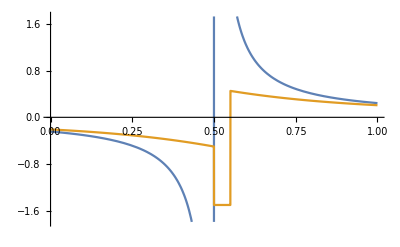

```mathematica
repl1={B->1.,θ->π/2+0.001,α->π};
{px->1/2 Tan[θ]#,f->-Sec[θ]#}&[-0.6ArcTan[10py]]
Plot[
{px/.%/.solpy/.sc->0.081/.repl1,
px/.FindRoot[syst/.repl1//N
,{{px,0.1,-1.5,1.5},{py,0.01,-20,20},{f,0.1,-10,10}}]},{A,0,1}]
```

Final solutions to use in Matlab:

```mathematica
{px->1/2 Tan[θ]#,f->-Sec[θ]#}&[-0.6ArcTan[10py]]
solpy/.sc->0.081
```

{px→-0.3 ArcTan[10 py] Tan[θ],f→0.6 ArcTan[10 py] Sec[θ]}

{py→0.081/(-2 A Sec[θ] Sin[α-1. θ]+Tan[θ])}

### 2-link, 2D - 2 points friction

```mathematica
$Assumptions=And@@(#>0&/@{F,B,A,r,Fn,px,py,α,θ,l1,l2})
```

F>0&&B>0&&A>0&&r>0&&Fn>0&&px>0&&py>0&&α>0&&θ>0&&l1>0&&l2>0

Friction Forces:

```mathematica
Plus@@(-py/(√((px-x)^2+py^2))/.x-> {-B/2,B/2})//FullSimplify
Plus@@((px-x)/(√((px-x)^2+py^2))/.x->{-B/2,B/2})//FullSimplify
Ff=Fn/2{%%,%}//FullSimplify
```

-py/(√((-B/2+px)^2+py^2))-py/(√((B/2+px)^2+py^2))

(-B/2+px)/(√((-B/2+px)^2+py^2))+(B+2 px)/(√((B+2 px)^2+4 py^2))

{1/2 Fn (-py/(√((-B/2+px)^2+py^2))-py/(√((B/2+px)^2+py^2))),1/2 Fn ((-B/2+px)/(√((-B/2+px)^2+py^2))+(B+2 px)/(√((B+2 px)^2+4 py^2)))}

```mathematica
Simplify[Ff/.py->0,Assumptions->B>0&& Abs[px]<B/2]
Simplify[Ff/.py->0,Assumptions->B>0&& px<-B/2]
```

{0,0}

{0,-Fn}

Friction Torque

```mathematica
τf=Fn/2 Plus@@(√((px-x)^2+py^2) /.x->{-B/2,B/2})//FullSimplify
```

1/2 Fn (√((-B/2+px)^2+py^2)+√((B/2+px)^2+py^2))

```mathematica
τ=({F Cos[θ],F Sin[θ],0}×{B/2+A Cos[α]-px,A Sin[α]-py,0})[[3]]//FullSimplify
τ/.{α->0,θ->π/2}
τ/.{α->π/2,θ->0}
```

-F py Cos[θ]+A F Sin[α-θ]-1/2 F (B-2 px) Sin[θ]

-A F-1/2 F (B-2 px)

A F-F py

Force balance:

```mathematica
syst={F Cos[θ]==-Ff[[1]],F Sin[θ]==-Ff[[2]],τf==-τ}
(*/.{√((B-2 px)^2+4 py^2)->l1,√((B+2 px)^2+4 py^2)->l2}*)
Solve[%,{px,py,F}]
```

```mathematica
syst1={F Cos[θ]==-1/2 Fn (-py/l1-py/l2),F Sin[θ]==-1/2 Fn ((-B/2+px)/l1+(B+2 px)/(2l2)),1/2 Fn (l1+l2)==F py Cos[θ]-A F Sin[α-θ]+1/2 F (B-2 px) Sin[θ],l1==√((-B/2+px)^2+py^2),l2==√((B/2+px)^2+py^2)};
Solve[syst1,{px,py,F,l1,l2}]
```

$Aborted

### Geometry calculations:

```mathematica
{α+β+β-ϕ==π,
2β+θ==π,
Sin[β-ϕ]/l==Sin[γ]/(2r Sin[θ/2])}
Eliminate[%//Normal,{β,ϕ}]
```

{α+2 β-ϕ==π,2 β+θ==π,Sin[β-ϕ]/l==(Csc[θ/2] Sin[γ])/(2 r)}

2 ArcSin[(l Csc[θ/2] Sin[γ])/(2 r)]==π-2 α+θ&&l≠0&&r≠0

```mathematica
(l  Sin[γ])/(2 r)==Sin[(π-2 α+θ)/2]Sin[θ/2]
Series[%,{θ,0,1}]
Solve[%//Normal,θ]
```

(l Sin[γ])/(2 r)==Sin[θ/2] Sin[1/2 (π-2 α+θ)]

(l Sin[γ])/(2 r)==1/2 Cos[α] θ+O[θ]^2

(θ→(l Sec[α] Sin[γ])/r)